## Task 6 Norm

```mathematica
a=1;
V=0.5;
tmin=0;
tmax=5;
Integrate[Exp[-a*t] +Sum[Integrate[Integrate[Exp[-a*t1]*V^2*Exp[-b*(t2-t1)]*Exp[-a*(t-t2)],{t1,0,t2}],{t2,0,t}],{b,{0.25,0.75}}],{t,tmin,tmax}]
ClearAll[a,V,tmin,tmax]
Integrate[Exp[-a*t] +Sum[Integrate[Integrate[Exp[-a*t1]*V^2*Exp[-b*(t2-t1)]*Exp[-a*(t-t2)],{t1,0,t2}],{t2,0,t}],{b,{0.25,0.75}}],{t,tmin,tmax}]//Simplify
```

1.77568

1/a^2(a (-ⅇ^(-a tmax)+ⅇ^(-a tmin))+1/(0.75-1. a)^2(-0.75 ⅇ^(-1. a tmax)+0.75 ⅇ^(-1. a tmin)+a ⅇ^(-1. a tmax) (2.-0.75 tmax)+a ⅇ^(-1. a tmin) (-2.+0.75 tmin)+a^2 (-1.33333 ⅇ^(-0.75 tmax)+1.33333 ⅇ^(-0.75 tmin)+1. ⅇ^(-1. a tmax) tmax-1. ⅇ^(-1. a tmin) tmin)) V^2+1/(0.25-1. a)^2(-0.25 ⅇ^(-1. a tmax)+0.25 ⅇ^(-1. a tmin)+a ⅇ^(-1. a tmax) (2.-0.25 tmax)+a ⅇ^(-1. a tmin) (-2.+0.25 tmin)+a^2 (-4. ⅇ^(-0.25 tmax)+4. ⅇ^(-0.25 tmin)+1. ⅇ^(-1. a tmax) tmax-1. ⅇ^(-1. a tmin) tmin)) V^2)

## Task 6 Q(t)

```mathematica
ClearAll[a,V]
Exp[-a*t] +Sum[Integrate[Integrate[Exp[-a*t1]*V^2*Exp[-b*(t2-t1)]*Exp[-a*(t-t2)],{t1,0,t2}],{t2,0,t}],{b,{0.25,0.75}}]//Simplify
```

ⅇ^(-a t)+(ⅇ^((-0.25-1. a) t) (1. ⅇ^(1. a t)+ⅇ^(0.25 t) (-1.+(0.25-1. a) t)) V^2)/(0.25-1. a)^2+(ⅇ^((-0.75-1. a) t) (1. ⅇ^(1. a t)+ⅇ^(0.75 t) (-1.+(0.75-1. a) t)) V^2)/(0.75-1. a)^2

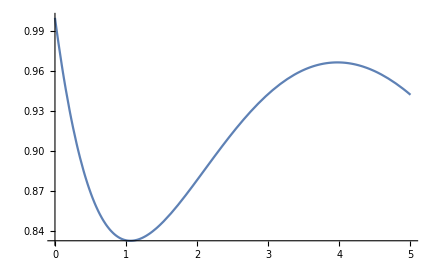

```mathematica
ClearAll[a,V]
a=0.4;
V=0.5;
Plot[Exp[-a*t] +Sum[Integrate[Integrate[Exp[-a*t1]*V^2*Exp[-b*(t2-t1)]*Exp[-a*(t-t2)],{t1,0,t2}],{t2,0,t}],{b,{0.25,0.75}}],{t,0,5}]
```

## I1 & I2

### I1

```mathematica
N[Integrate[Exp[-0.5*t]*t,{t,0,5}]]
N[Integrate[Exp[-1*t]*t,{t,0,5}]]
```

2.85081

0.959572

### I2

```mathematica
N[Integrate[Exp[-0.5*t]*t^2,{t,0,5}]]
N[Integrate[Exp[-1*t]*t^2,{t,0,5}]]
```

7.29899

1.7507